# Числено диференциране

## Параметрите a и b са съответно предпоследната и последната цифра от факултетния номер

1. Да се състави таблица за функцията
 f(α) = cos (α + π/(a+b+1)) , α ∈ [−π, π]
като разделите интервала така, че да се получат общо 6 възела.
2. Да се намерят първите производни f' във всички възли.
3. Да се намерят първите производни f'' във всички възли.

## Генериране на данни

```mathematica
a = -π; b = π;
n = 5;
N[h = (b - a)/n]
```

1.25664

```mathematica
N[xt = Table[a + i *h, {i, 0,n}]]
```

{-3.14159,-1.88496,-0.628319,0.628319,1.88496,3.14159}

```mathematica
f[x_] := Cos[x + π/14]
N[yt = f[xt]]
```

{-0.974928,-0.0896393,0.919528,0.657939,-0.512899,-0.974928}

```mathematica
h = 1.25664
```

1.25664

```mathematica
n = Length[xt]
```

6

## Формули с точност O(h^2) - втори порядък

### Първа производна

Попълваме средните точки

```mathematica
yp2 = Table[(yt[[i+1]] - yt[[i-1]])/(2h), {i, 2, n - 1}]
```

{0.753778,0.297451,-0.569943,-0.649695}

Допълваме производната в десния край (последната)

```mathematica
AppendTo[yp2, (yt[[n - 2]] - 4yt[[n-1]] + 3yt[[n]])/(2h)]
```

{0.753778,0.297451,-0.569943,-0.649695,-0.0856442}

Допълваме производната в левия край (първата)

```mathematica
PrependTo[yp2, (-3yt[[1]] +4yt[[2]] - yt[[3]])/(2h)]
```

{0.655199,0.753778,0.297451,-0.569943,-0.649695,-0.0856442}

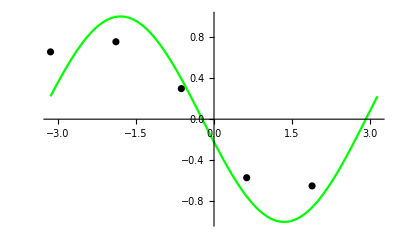

```mathematica
pointsyp2 = Table[{xt[[i]], yp2[[i]]}, {i , 1, n-1}] ;
gryp2 = ListPlot[pointsyp2, PlotStyle->Black];
grfyp = Plot[f'[x], {x, xt[[1]], xt[[n]]}, PlotStyle->Green];
Show[grfyp, gryp2]
```

### Втора производна

Попълваме средните точки

```mathematica
ypp2 = Table[(yt[[i+1]] -2 yt[[i]]+yt[[i-1]])/h^2, {i, 2, n - 1}]
```

{0.0784466,-0.804712,-0.575786,0.448857}

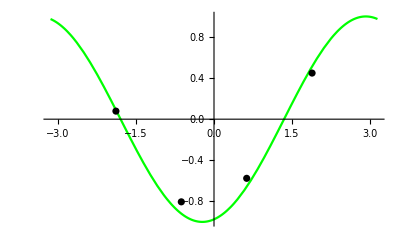

```mathematica
pointsypp2 = Table[{xt[[i + 1]], ypp2[[i]]}, {i , 1, n-2}] ;
grypp2 = ListPlot[pointsypp2, PlotStyle->Black];
grfypp = Plot[f''[x], {x, xt[[1]], xt[[n]]}, PlotStyle->Green];
Show[grfypp, grypp2]
```